Codigo realizado para el proyecto final de Biologica Sintetica. 
Realizado por Sergio Daniel Hernandez y Nancy Estefanía Ruiz
Referencia: http://www.mathematica-journal.com/data/uploads/2011/05/Voelkl.pdf

```mathematica
Manipulate[showpop[evolution⟦u⟧],{{u,1},1,dynamic[Length[evolution]],1,Appearance ->"Labeled"},AutorunSequencing ->{1},SynchronousInitialization -> False,Initialization :> (
Quiet@Get["Combinatorica`"];
initial[n_,i_]:=Join[Table[1,{i}],Table[0,{n-i}]];
update[pop_List]:=Module[{repro,elim},{repro,elim} =RandomInteger[{1,Length[pop]},2];
ReplacePart[pop,elim -> pop⟦repro⟧]];
moran[n_,i_]:=NestWhileList[update,initial[n,i],n>Total[#]>0&];
showpop[pop_]:=Module[{g},g=Combinatorica`SetVertexWeights[Combinatorica`CompleteGraph[Length[pop]],pop];
GraphPlot[g,EdgeRenderingFunction -> None,VertexRenderingFunction ->
({If[Combinatorica`GetVertexWeights[g]⟦#2⟧ ==0,Hue[0,0.8,0.7],Hue[0.7,0.8,0.7]],PointSize[0.08],Point[#]}&),ImageSize -> 280,PlotLabel->"Poblacion de bacterias con mismo fitness"]];
evolution=moran[30,15];
If[u>Length[evolution],u=Length[evolution]]
)]
```

```mathematica
Manipulate[showpopRel[evolution2⟦u⟧,2.05],{{u,1},1,Dynamic[Length[evolution2]],1,Appearance -> "Labeled"},AutorunSequencing -> {1},SynchronousInitialization -> False,Initialization :> (
Quiet@Get["Combinatorica`"];
initial[n_,i_]:=Join[Table[1,{i}],Table[0,{n-i}]];
updateRel[pop_List,r_]:=Module[{j,reprod,elimPos},j=Total[pop];
reprod=r j /(r j+Length[pop]-j);
elimPos=RandomInteger[{1,Length[pop]}];
ReplacePart[pop,elimPos -> RandomChoice[{1-reprod,reprod}-> {0,1}]]];
moranRel[n_,i_,r_]:=NestWhileList[updateRel[#,r]&,initial[n,i],n>Total[#]>0&];
showpopRel[pop_,r_]:=Module[{g},g=Combinatorica`SetVertexWeights[Combinatorica`CompleteGraph[Length[pop]],pop];
GraphPlot[g,EdgeRenderingFunction -> None,VertexRenderingFunction ->
(Flatten[{If[Combinatorica`GetVertexWeights[g]⟦#2⟧ == 0,{Hue[0,0.8,0.7],PointSize[0.016]},{Hue[0.7,0.8,0.7],PointSize[0.016 Sqrt[r]]}],Point[#]}]&),ImageSize -> 480,PlotLabel->"Poblacion de E.Coli. Transgenico"]];
evolution2=moranRel[90,45,2.05];
If[u>Length[evolution2],u=Length[evolution2]]
)]
```

```mathematica
Manipulate[showpopRel[evolution3⟦u⟧,1.558],{{u,1},1,Dynamic[Length[evolution3]],1,Appearance -> "Labeled"},AutorunSequencing -> {1},SynchronousInitialization -> False,Initialization :> (
Quiet@Get["Combinatorica`"];
initial[n_,i_]:=Join[Table[1,{i}],Table[0,{n-i}]];
updateRel[pop_List,r_]:=Module[{j,reprod,elimPos},j=Total[pop];
reprod=r j /(r j+Length[pop]-j);
elimPos=RandomInteger[{1,Length[pop]}];
ReplacePart[pop,elimPos -> RandomChoice[{1-reprod,reprod}-> {0,1}]]];
moranRel[n_,i_,r_]:=NestWhileList[updateRel[#,r]&,initial[n,i],n>Total[#]>0&];
showpopRel[pop_,r_]:=Module[{g},g=Combinatorica`SetVertexWeights[Combinatorica`CompleteGraph[Length[pop]],pop];
GraphPlot[g,EdgeRenderingFunction -> None,VertexRenderingFunction ->
(Flatten[{If[Combinatorica`GetVertexWeights[g]⟦#2⟧ == 0,{Hue[0,0.8,0.7],PointSize[0.016]},{Hue[0.7,0.8,0.7],PointSize[0.016 Sqrt[r]]}],Point[#]}]&),ImageSize -> 480,PlotLabel->"Poblacion de Salmonella Transgenica"]];
evolution3=moranRel[90,45,1.558];
If[u>Length[evolution3],u=Length[evolution3]]
)]
```

```mathematica
Manipulate[showpopRel[evolution4⟦u⟧,1.2],{{u,1},1,Dynamic[Length[evolution4]],1,Appearance -> "Labeled"},AutorunSequencing -> {1},SynchronousInitialization -> False,Initialization :> (
Quiet@Get["Combinatorica`"];
initial[n_,i_]:=Join[Table[1,{i}],Table[0,{n-i}]];
updateRel[pop_List,r_]:=Module[{j,reprod,elimPos},j=Total[pop];
reprod=r j /(r j+Length[pop]-j);
elimPos=RandomInteger[{1,Length[pop]}];
ReplacePart[pop,elimPos -> RandomChoice[{1-reprod,reprod}-> {0,1}]]];
moranRel[n_,i_,r_]:=NestWhileList[updateRel[#,r]&,initial[n,i],n>Total[#]>0&];
showpopRel[pop_,r_]:=Module[{g},g=Combinatorica`SetVertexWeights[Combinatorica`CompleteGraph[Length[pop]],pop];
GraphPlot[g,EdgeRenderingFunction -> None,VertexRenderingFunction ->
(Flatten[{If[Combinatorica`GetVertexWeights[g]⟦#2⟧ == 0,{Hue[0,0.8,0.7],PointSize[0.016]},{Hue[0.7,0.8,0.7],PointSize[0.016 Sqrt[r]]}],Point[#]}]&),ImageSize -> 480,PlotLabel->"Poblacion de R.Rhodnii Transgenico"]];

evolution4=moranRel[90,45,1.2];
If[u>Length[evolution4],u=Length[evolution4]]
)]
```

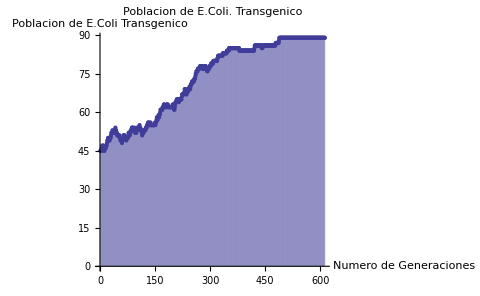

```mathematica
X=moranRel[90,45,2.05];
lista=Array[f,Length[X]];
For[k=1,k<Length[X],k++,f[k]=Count[X[[k]],1]];
ListPlot[lista,Filling->Axis,PlotLabel->"Poblacion de E.Coli. Transgenico",AxesLabel->{"Numero de Generaciones","Poblacion de E.Coli Transgenico"},ImageSize -> 480]
```

$Aborted

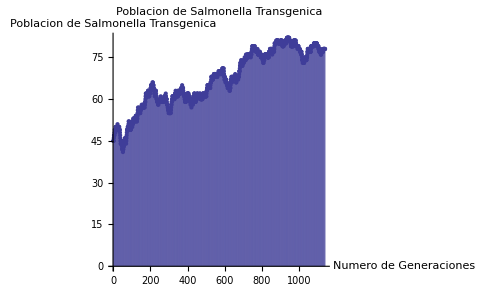

```mathematica
Y=moranRel[90,45,1.558];
lista=Array[f,Length[Y]];
For[h=1,h<Length[Y],k++,f[h]=Count[Y[[h]],1]];
ListPlot[lista,Filling->Axis,PlotLabel->"Poblacion de Salmonella Transgenica",AxesLabel->{"Numero de Generaciones","Poblacion de Salmonella Transgenica"},ImageSize -> 480]
```

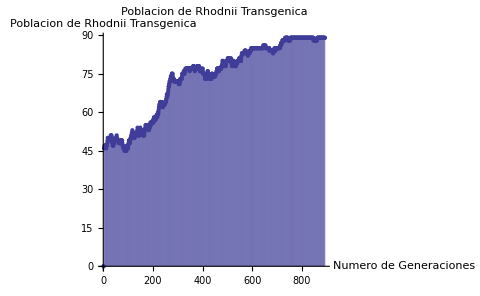

```mathematica
Z=moranRel[90,45,1.2];
lista=Array[f,Length[Z]];
For[l=1,l<Length[Z],l++,f[l]=Count[Z[[l]],1]];
ListPlot[lista,Filling->Axis,PlotLabel->"Poblacion de Rhodnii Transgenica",AxesLabel->{"Numero de Generaciones","Poblacion de Rhodnii Transgenica"},ImageSize -> 480]
```

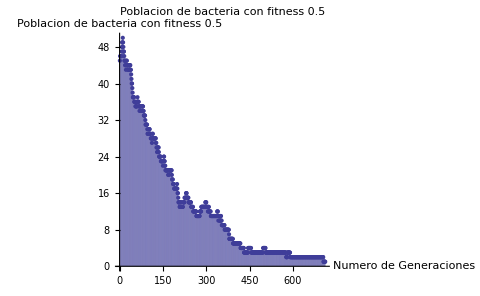

```mathematica
W=moranRel[90,45,0.5];
lista=Array[f,Length[W]];
For[m=1,m<Length[W],m++,f[m]=Count[W[[m]],1]];
ListPlot[lista,Filling->Axis,PlotLabel->"Poblacion de bacteria con fitness 0.5",AxesLabel->{"Numero de Generaciones","Poblacion de bacteria con fitness 0.5"},ImageSize -> 480]
```